```mathematica
y=Import["c:\\o1.txt","Table"];
XY=Import["c:\\o2.txt","Table"];
ys=Import["c:\\o3.txt","Table"];
```

```mathematica
yw=Differences[Transpose[y][[2]]]/(y[[100,2]]-y[[84,2]]);
```

```mathematica
d=Table[{y[[i,1]],yw[[i]]},{i,Length[yw]}];
```

```mathematica
f=Interpolation[y];
```

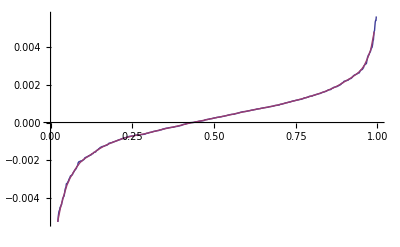

```mathematica
ListPlot[{XY,y},Joined->True]
```

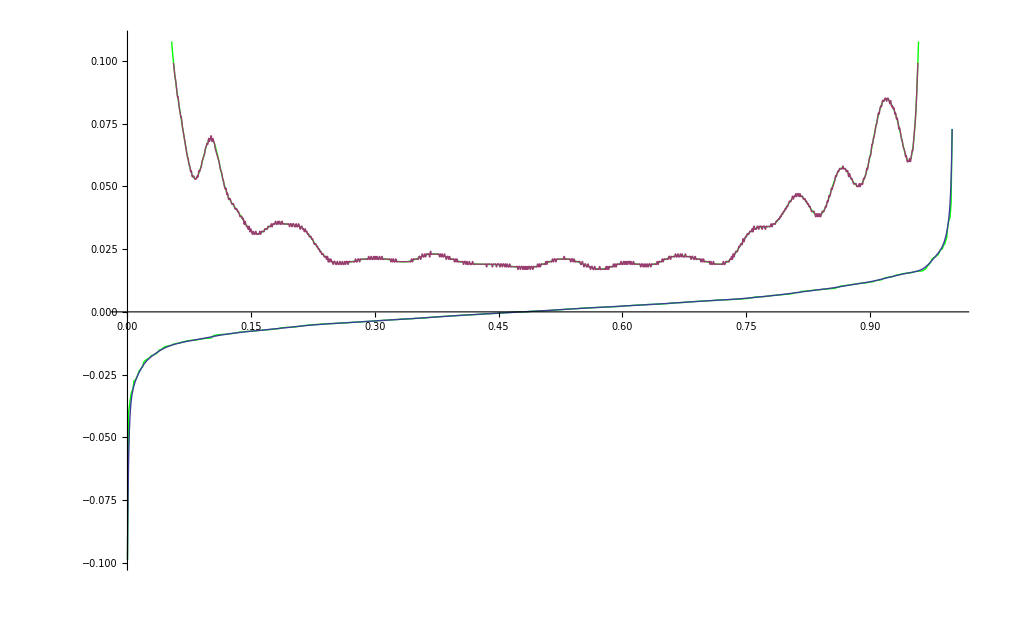

```mathematica
Show[ListPlot[{XY,ys},Joined->True,PlotStyle->Green],Plot[{f[x],f'[x]},{x,0,1}]]
```

```mathematica
w=Import["c:\\RandA.txt","Table"];
```

```mathematica
W=Transpose[Transpose[w][[1;;2]]];Abl=Transpose[{Transpose[w][[1]],Transpose[w][[3]]}];zwAbl=Transpose[{Transpose[w][[1]],Transpose[w][[4]]}];
```

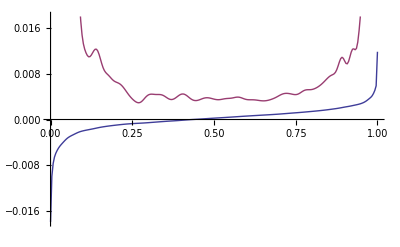

```mathematica
ListPlot[{W,Abl},Joined->True]
```